```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### Range of densities

```mathematica
{triggermass[0.85],triggermass[1.37]}
```

{0.00337513,0.0000124363}

```mathematica
{Massreverse[0.85],Massreverse[1.25],Massreverse[1.37]}
```

{7.1606,8.46005,9.50943}

```mathematica
{Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->7.16},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->8.46},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->9.5}}
```

{(7.20147×10^29)/Centimeter^3,(1.43688×10^31)/Centimeter^3,(1.57551×10^32)/Centimeter^3}

```mathematica
6*{(7.201468136264897*^29)/Centimeter^3,(1.4368817984738546*^31)/Centimeter^3,(1.5755095624615844*^32)/Centimeter^3}
```

{(4.32088×10^30)/Centimeter^3,(8.62129×10^31)/Centimeter^3,(9.45306×10^32)/Centimeter^3}

```mathematica
Convert[9.453057374769507*^32 Centimeter^-3(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

7.56245 ElectronVolt^3 Mega^3

WD data

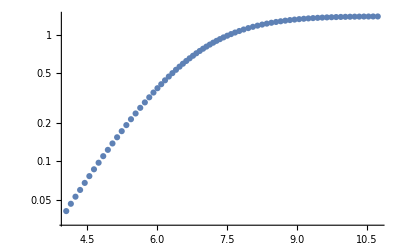

```mathematica
ListLogPlot[WD]
```

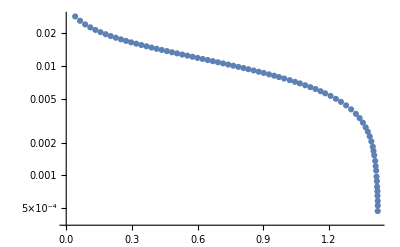

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0235528

```mathematica
vesc[0.85]
```

0.0140142

```mathematica
Radplot[1.40]
```

0.00185935

```mathematica
vesc[1.42]
```

0.0610014

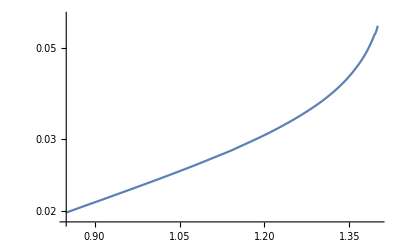

```mathematica
LogPlot[vesc[M],{M,0.85,1.4}]
```

#### trigger size, E_boom (GeV)

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
10^logρ Convert[Gram/Centimeter^3 1/(12 Giga ElectronVolt/SpeedOfLight^2)*(200 Mega ElectronVolt Fermi)^3,(Mega ElectronVolt)^3]*(1/(Mega ElectronVolt))^3;
nionMeV[M_]:=Convert[10^Massreverse[M] Gram/Centimeter^3*SpeedOfLight^2/(12Giga ElectronVolt)*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]*1/(Mega ElectronVolt)^3
nionMeV2[logρ_]:=3.7397260789901873*^-10 10^logρ
eboom[M_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(triggermass[M](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV[M],Z->6})]
eboomdensity[logρ_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(trigger[10^logρ](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV2[logρ],Z->6})]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,None},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_⊙)","ℰ_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> {Directive[Bold],Medium},ImageSize->Large];
```

#### How much of the WD detector should we observe?

```mathematica
restrict=1/2;
```

#### SN information

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 (4π)/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[1.25] (4π)/3(Radplot[1.25]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

#### DM Wind - Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3(Rwd*restrict)^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

2.87303×10^-20

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

4.59686×10^-27

```mathematica
eboom[1.4]
```

15.0338

```mathematica
(Log10[unitlesscollision 1/integralcollision[15.04]]/.logmdm->15.04)
```

-16.6446

```mathematica
Table[{logmdm,Log10[unitlesscollision 1/integralcollision[logmdm]]},{logmdm,15.04,24,0.1}];
```

$Aborted

```mathematica
SNlist={{15.04,-16.10406176129751},{15.139999999999999,-17.172399046810057},{15.239999999999998,-17.291977329160385},{15.34,-17.292168309046474},{15.44,-17.24315844948377},{15.54,-17.204526058483797},{15.639999999999999,-17.214178641793193},{15.739999999999998,-17.191167884183987},{15.84,-17.19198571688968},{15.94,-17.18622987721764},{16.04,-17.1869120551312},{16.14,-17.199547138311367},{16.24,-17.218634919596216},{16.34,-17.250999604393925},{16.439999999999998,-17.294111333374023},{16.54,-17.347238299142795},{16.64,-17.41419384266277},{16.74,-17.482208618206958},{16.84,-17.562068159874723},{16.939999999999998,-17.65044375555382},{17.04,-17.743089164157265},{17.14,-17.839315526309125},{17.24,-17.937722097954524},{17.34,-18.038769966686523},{17.439999999999998,-17.975451222862187},{17.54,-17.849595363164497},{17.64,-17.7110444768282},{17.74,-17.572148396772256},{17.84,-17.432690310794737},{17.939999999999998,-17.293532988828026},{18.04,-17.15408243113624},{18.14,-17.015483957841823},{18.24,-16.87671637990075},{18.34,-16.738976164649046},{18.439999999999998,-16.60085088332797},{18.54,-16.46334864820152},{18.64,-16.325318605592454},{18.74,-16.18738392111567},{18.84,-16.049068491692918},{18.939999999999998,-15.91049875914166},{19.04,-15.77172048843425},{19.14,-15.632431729604466},{19.24,-15.49295363259842},{19.34,-15.35287219889305},{19.439999999999998,-15.212495521044529},{19.54,-15.07176863984791},{19.64,-14.930598726671715},{19.74,-14.78953668182063},{19.84,-14.64797553376806},{19.939999999999998,-14.50623649653608},{20.04,-14.364021599992506},{20.14,-14.22115719133776},{20.24,-14.077599905133166},{20.34,-13.93333797053565},{20.439999999999998,-13.788402876276049},{20.54,-13.643150562657862},{20.64,-13.497413050434492},{20.74,-13.351457259907141},{20.84,-13.205198832750712},{20.939999999999998,-13.058292134333728},{21.04,-12.910782296523378},{21.14,-12.762505718485759},{21.24,-12.613412245599832},{21.34,-12.463559876734976},{21.439999999999998,-12.313036262805307},{21.54,-12.16175487599537},{21.64,-12.00974471698437},{21.74,-11.857004540104834},{21.84,-11.703381486648412},{21.939999999999998,-11.54887739522484},{22.04,-11.393399255587388},{22.14,-11.2370535738019},{22.24,-11.07162583960384},{22.34,-10.871625839603837},{22.439999999999998,-10.671625839603841},{22.54,-10.471625839603838},{22.64,-10.271625839603836},{22.74,-10.07162583960384},{22.84,-9.871625839603837},{22.939999999999998,-9.671625839603841},{23.04,-9.471625839603838},{23.14,-9.271625839603836},{23.240000000000002,-9.071625839603833},{23.34,-8.871625839603837},{23.439999999999998,-8.671625839603841},{23.54,-8.471625839603838},{23.64,-8.271625839603836},{23.740000000000002,-8.071625839603833},{23.84,-7.871625839603837},{23.939999999999998,-7.671625839603841}};
```

```mathematica
collisionSNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlist][23.5]+2(logmdm-23.5),Interpolation[SNlist][logmdm]]
SNcollision=Plot[collisionSNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
eboomlimitcollisionf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-100,10}];
eboomlimitcollisionf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-100,10}];
collisionlimitSN=Plot[( 100 Sign[x-eboom[1.40]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.0065],Black}],PlotRange->{-16.104061761297505,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];
XLabelCollision={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"},{18,"10^18"},{20,"10^20"},{22,"10^22"},{24,"10^24"},{26,"10^26"},{28,"10^28"},{30,"10^30"}};
YLabelCollision={{-80,"10^-80"},{-75,"10^-75"},{-70,"10^-70"},{-65,"10^-65"},{-60,"10^-60"},{-55,"10^-55"},{-50,"10^-50"},{-45,"10^-45"},{-40,"10^-40"},{-35,"10^-35"},{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"}};
canvascollisionf1=Plot[-100,{logmdm,15.1,25},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "σ_χχ (cm^2)"},LabelStyle-> {Directive[Bold],Medium},PlotRange->{-28,1},Axes->None];
```

```mathematica
SNcollisionregionplot=RegionPlot[{Log10[σHalo]>σ>collisionSNwhole[logmdm]},{logmdm,15.04,30},{σ,-20,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9717} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

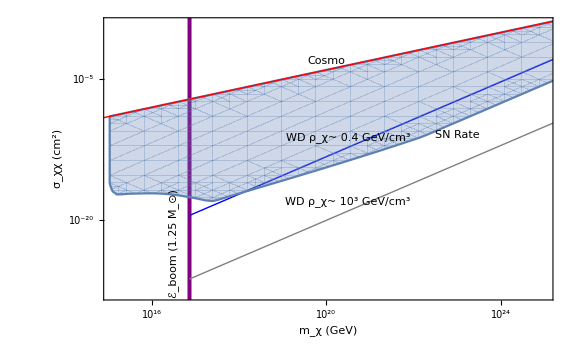

```mathematica
collisionobservation=Show[canvascollisionf1,eboomlimitcollisionf1,RXcollision, NuStarcollision,SNcollisionregionplot,σHaloplot,Graphics[Inset[Style["WD ρ_χ~ 0.4 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{20.5,-11.2},{0,0},10,{1,1/2.5}]],Graphics[Inset[Style["WD ρ_χ~ 10^3 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{20.5,-18.1},{0,0},10,{1,1/2.5}]],Graphics[Inset[Style["SN Rate",Medium,Black,FontFamily->"Helvetica"],{23,-11},{0,0},10,{1,1/2}]],Graphics[Inset[Style["ℰ_boom (1.25 M_⊙)",Medium,Black,FontFamily->"Helvetica"],{16.5,-22.5},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Medium,Black,FontFamily->"Helvetica"],{20,-3},{0,0},10,{1,1/3}]],ImageSize->Large]
```

#### DM Wind - Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3(Rwd restrict)^3;
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

3.15562×10^11

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

7.88906×10^14

```mathematica
Log10[unitlessdecay integraldecay[15.04]]/.logmdm->15.04
```

5.06183

```mathematica
SNlistdecay=Table[{logmdm,Log10[unitlessdecay integraldecay[logmdm]]},{logmdm,15.04,24,0.1}];
```

$Aborted

```mathematica
SNlistdecay
```

```mathematica
SNlistdecay={{15.04,5.061829204847497},{15.139999999999999,6.214449275371579},{15.239999999999998,6.420589455810837},{15.34,6.510461040359902},{15.44,6.551544112979498},{15.54,6.598983262457922},{15.639999999999999,6.6856613499137305},{15.739999999999998,6.739440702499228},{15.84,6.810654823208336},{15.94,6.87409651751223},{16.04,6.941603890234163},{16.14,7.018476255467032},{16.24,7.100924160863706},{16.34,7.195626583705712},{16.439999999999998,7.301378901121159},{16.54,7.41810524681221},{16.64,7.54973122020263},{16.74,7.685465761743471},{16.84,7.834576812918031},{16.939999999999998,7.994203637136746},{17.04,8.160348433582529},{17.14,8.33212650625868},{17.24,8.508515604189945},{17.34,8.68944064906932},{17.439999999999998,8.717377216011768},{17.54,8.68690718694907},{17.64,8.644664523237047},{17.74,8.602230683947052},{17.84,8.559395960846766},{17.939999999999998,8.51696563349105},{18.04,8.474353931738168},{18.14,8.43261081928965},{18.24,8.390759744502407},{18.34,8.349933933008959},{18.439999999999998,8.308791626797166},{18.54,8.26830106438931},{18.64,8.227370599695131},{18.74,8.186595386189007},{18.84,8.145522491925444},{18.939999999999998,8.104275333651207},{19.04,8.06289985152446},{19.14,8.02110489008738},{19.24,7.979195254970561},{19.34,7.9367661371903155},{19.439999999999998,7.894108112253941},{19.54,7.851166934406992},{19.64,7.8078527462422915},{19.74,7.764699029448229},{19.84,7.721122618226387},{19.939999999999998,7.677434099756068},{20.04,7.633345861905258},{20.14,7.5886904443392265},{20.24,7.543425648510447},{20.34,7.497537414166098},{20.439999999999998,7.451052903816492},{20.54,7.404311306028331},{20.64,7.357146431243585},{20.74,7.309819417282067},{20.84,7.262253460809001},{20.939999999999998,7.214119075568504},{21.04,7.165459681707677},{21.14,7.116111599627434},{21.24,7.066012862544948},{21.34,7.015215771441305},{21.439999999999998,6.963808844192963},{21.54,6.911716347424954},{21.64,6.858982016750252},{21.74,6.805603420150687},{21.84,6.751421635511648},{21.939999999999998,6.6964179758545805},{22.04,6.640493313700964},{22.14,6.583753107612602},{22.24,6.518052789531721},{22.34,6.418052789531719},{22.439999999999998,6.3180527895317224},{22.54,6.218052789531721},{22.64,6.11805278953172},{22.74,6.018052789531722},{22.84,5.91805278953172},{22.939999999999998,5.8180527895317224},{23.04,5.718052789531721},{23.14,5.61805278953172},{23.240000000000002,5.518052789531718},{23.34,5.41805278953172},{23.439999999999998,5.3180527895317224},{23.54,5.218052789531721},{23.64,5.11805278953172},{23.740000000000002,5.018052789531717},{23.84,4.91805278953172},{23.939999999999998,4.8180527895317224}};
```

```mathematica
decaySNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlistdecay][23.5]-(logmdm-23.5),Interpolation[SNlistdecay][logmdm]]
```

```mathematica
SNdecay=Plot[decaySNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];eboomlimitdecayf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,50},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{0,50}];
eboomlimitdecayf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{3.5,20}];
decaylimitSN=Plot[(100 Sign[x-eboom[1.4]]),{x,14,50},ExclusionsStyle->Directive[{Thickness[.006],Black}],PlotRange->{-10,5.061829204847496}];
YLabelDecay={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}};
canvasdecayf1=Plot[-100,{logmdm,15,24},Frame->True,FrameTicks->{{YLabelDecay,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "τ_χ (Gyr)"},LabelStyle-> {Directive[Bold],Medium},PlotRange->{1.3,15},Axes->None];
```

```mathematica
SNdecayregionplot=RegionPlot[{2≤τ≤decaySNwhole[logmdm]},{logmdm,15.04,30},{τ,0,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

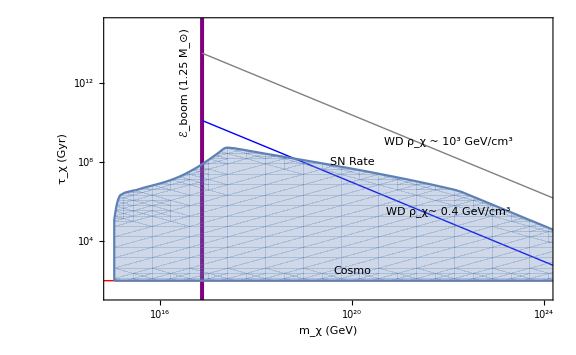

```mathematica
decayobservation=Show[canvasdecayf1,eboomlimitdecayf1,RXdecay,NuStardecay,SNdecayregionplot,τCosmoplot,Graphics[Inset[Style["WD ρ_χ~ 0.4 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{22,5.5},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["WD ρ_χ ~ 10^3 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{22,9},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["SN Rate",Medium,Black,FontFamily->"Helvetica"],{20,8},{0,0},10,{1,-1/10}]],Graphics[Inset[Style["ℰ_boom (1.25 M_⊙)",Medium,Black,FontFamily->"Helvetica"],{16.5,12},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Medium,Black,FontFamily->"Helvetica"],{20,2.5},{0,0},10,{1,0}]],ImageSize->Large]
```

#### Transit Constraints, ϵ (in MeV!) released per collision

```mathematica
transitboom[M_]:=(((10^eboom[M] 10^3)MeV)/(nionMeV[M] MeV^3(triggermass[M]cm*(200 MeV*10^-13 cm)^-1))1/(1 ϵ MeV)(200 MeV *10^-13 cm)^2)1/cm^2;
```

```mathematica
transitreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^6},{M,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

Convert::incomp: Incompatible units in (5.8088×10^28 ElectronVolt Giga Meter^3)/(Centimeter^3 Second snrate) and ElectronVolt Giga.

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

#### Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Null

#### Null

```mathematica
Null
```

#### Null

```mathematica
Null
```

Null

#### Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null